Homework #3
Cagatay Duygu - 48369962

```mathematica
Quit[]
```

Problem #3.15

-Graphics-

```mathematica
A=({{0, 1}, {-1, 1}}); 
B=({{0}, {1}});
```

```mathematica
Eigensystem[A]
```

{{1/2 (1+ⅈ √3),1/2 (1-ⅈ √3)},{{-1/2 ⅈ (ⅈ+√3),1},{1/2 ⅈ (-ⅈ+√3),1}}}

Approximate Poles (Open-Loop)

```mathematica
eig = Eigenvalues[A]// N
```

{0.5+0.866025 ⅈ,0.5-0.866025 ⅈ}

Closed - loop poles (Optimal)

Since r -> ∞ , optimal closed loop poles are the reflection of open loop poles.
Because of that,

```mathematica
clpoles= -eig
```

{-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ}

Characteristic polynomial (Optimal):

```mathematica
α=(s-clpoles[[1]])(s-clpoles[[2]])
```

((0.5-0.866025 ⅈ)+s) ((0.5+0.866025 ⅈ)+s)

C-L GAINS

```mathematica
KK=({{k1, k2}});
```

```mathematica
KK
```

{{k1,k2}}

```mathematica
II=({{1, 0}, {0, 1}});
```

```mathematica
δ=Det[s II-(A-B.KK)]
```

1+k1-s+k2 s+s^2

```mathematica
ksolved=SolveAlways[δ==α,{s}]//Chop
```

{{k1→0,k2→2.}}

```mathematica
Koptimal=KK/.ksolved//Flatten
```

{0,2.}

Problem #3.17

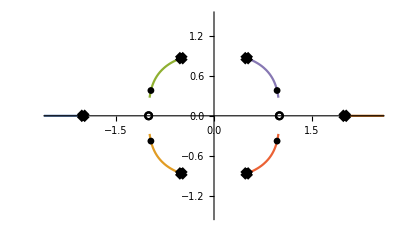

```mathematica
Tf[s_]:=((s+1)(s-1))/((s^2-s+1)(s+2))
H[s_]:=1/r((Numerator[Tf[s]] Numerator[Tf[-s]])/(Denominator[Tf[s]] Denominator[Tf[-s]]))
RootLocusPlot[H[s]/.r^-1->k,{k,0,30}, PlotRange->{{-2.5,2.5},{-1.5,1.5}}]
```

OPEN-LOOP

```mathematica
zerosOL=s/.Solve[Numerator[Tf[s]]==0,s]
```

{-1,1}

```mathematica
polesOL=s/.Solve[Denominator[Tf[s]]==0,s]//N
```

{-2.,0.5+0.866025 ⅈ,0.5-0.866025 ⅈ}

b) CLOSED-LOOP (r->0)

Reflection: -1,-1
3rd pole --> -(infinity)

For non-zero (small) r value:
b_0=1

```mathematica
Exponent[Denominator[Tf[s]],s]-Exponent[Numerator[Tf[s]],s]
```

n-m

1

-Graphics-

c) CLOSED-LOOP (r→∞)

Reflection:

```mathematica
polesCL1=-polesOL[[2]]
```

-0.5-0.866025 ⅈ

```mathematica
polesCL2=-polesOL[[3]]
```

-0.5+0.866025 ⅈ

```mathematica
polesCL3=polesOL[[1]]
```

-2.